```mathematica
Quit[]
```

Declaring Constants All in GeV

```mathematica
Me=.000511;
Mμ=.1057;
Mτ=1.777;
MW=80.4;
Mu= 0.0023;
Md= 0.0048;
Ms = 0.095;
Mc = 1.4;
Mt = 172;
Mb  = 4.2;
MZ=91;
v=246;
Gμ=1.16637*10^-5;
α=1/128;
αs = .1172;
cw =√(1-.23126);
sw = √0.23126;
Bem=-11/3;
Bg=7;
```

This is the function of Rg and Rgamma

```mathematica
Tau[M_,Mx_]:= 4 M^2/Mx^2;
ft[τ_]:=Piecewise[{{ArcSin[√(1/τ)]^2, τ≥1}, {-1/4 (Log[(1+√(1-τ))/(1-√(1-τ))]-ⅈ π)^2, τ<1}}]
F1[tau1_]:=2+3tau1+(3tau1)*(2-tau1) ft[tau1];
F12[tau12_]:= -2tau12(1+(1-tau12) ft[tau12]);
SumLoopCorrectionRγ[Mx_]:=       F12[Tau[Me,Mx]]+F12[Tau[Mμ,Mx]]+F12[Tau[Mτ,Mx]]+F1[Tau[MW,Mx]] + 3(2/3)^2 F12[Tau[Mu,Mx]]+3(-1/3)^2 F12[Tau[Md,Mx]]+ 3(2/3)^2 F12[Tau[Mc,Mx]]+3(-1/3)^2 F12[Tau[Ms,Mx]]+ 3(2/3)^2 F12[Tau[Mt,Mx]]+3(-1/3)^2 F12[Tau[Mb,Mx]];
SumLoopCorrectionRg[Mx_]:=F12[Tau[Mu,Mx]]+F12[Tau[Md,Mx]]+F12[Tau[Ms,Mx]]+F12[Tau[Mc,Mx]]+F12[Tau[Mt,Mx]]+F12[Tau[Mb,Mx]];
Rg[Mx_]:=Abs[-Bg+1/2 SumLoopCorrectionRg[Mx]]^2/Abs[1/2 SumLoopCorrectionRg[Mx]]^2;
Rγ[Mx_]:=Abs[-Bem+SumLoopCorrectionRγ[Mx]]^2/Abs[SumLoopCorrectionRγ[Mx]]^2
Plot[{Rγ[Mx],Rg[Mx]/100},{Mx,20,200},PlotRange ->{{20,200},{0,3}},PlotLegends->"Expressions",Frame->True, AxesOrigin->{20,0},PlotLabel->"Rg and Rγ",Exclusions-> None]
Plot[Rg[Mx]/100,{Mx,200,1000},PlotRange ->{{200,1000},{.4,1.6}},PlotLegends->"Expressions",Frame->True, AxesOrigin->{20,0},PlotLabel ->"Rg",Exclusions-> None]
Plot[{Rg[Mx]*Rγ[Mx]},{Mx,20,200}];
```

Higgs Gamma Gamma and Higgs Gluon Gluon decay

```mathematica
TauH[M_,Mh_]:= Mh^2/(4 M^2);
ftH[τ_]:=Piecewise[{{ArcSin[√τ]^2, τ≤1}, {-1/4(Log[(1+√(1-τ^-1))/(1-√(1-τ^-1))]-ⅈ*π)^2, τ>1}}]
A12H[tauHi_]:=2(tauHi+(tauHi-1)*ftH[tauHi])*(tauHi)^-2
A1H[tauHi_]:=-(2(tauHi)^2+3tauHi+3(2tauHi-1)*ftH[tauHi])tauHi^-2;
SumFermionsAndWHiggs[Mh_]:=A12H[TauH[Me,Mh]]+A12H[TauH[Mμ,Mh]]+A12H[TauH[Mτ,Mh]]+A1H[TauH[MW,Mh]] + 3(2/3)^2 A12H[TauH[Mu,Mh]]+3(-1/3)^2 A12H[TauH[Md,Mh]]+ 3(2/3)^2 A12H[TauH[Mc,Mh]]+3(-1/3)^2 A12H[TauH[Ms,Mh]]+ 3(2/3)^2*A12H[TauH[Mt,Mh]]+3(-1/3)^2 A12H[TauH[Mb,Mh]];
WidthHγγ[Mh_]:=(Gμ α^2 Mh^3)/(128 √2 π^3)Abs[SumFermionsAndWHiggs[Mh]]^2;
LogLogPlot[Re[WidthHγγ[Mh]]*1000000,{Mh,100,1000},PlotRange ->{{100,1000},{1,150}}PlotLegends->"Expressions",AxesLabel -> {Hx,WidthHγγ},AxesOrigin->{100,0},PlotLabel ->"Width of Higgs Gamma Gamma Decay",Exclusions-> None,MaxRecursion->5]
SumQuarks[Mh_]:=A12H[taubH[Mh]]+A12H[tautH[Mh]];
WidthHgg[Mh_]:= (Gμ αs^2 Mh^3)/(36 √2 π^3)Abs[(3/4)* SumQuarks[Mh]]^2;
LogLogPlot[WidthHgg[Mh]*1000,{Mh,100,1000},PlotLegends->"Expressions",AxesLabel -> {Mh,WidthHgg},AxesOrigin->{100,0},PlotLabel ->"Width of Higgs Gluon Gluon Decay" ,Exclusions->None,MaxRecursion->5]
```

WIdth of the Dilaton for GG and gamma gamma

```mathematica
WidthXγγ[Mx_,f_]:=Rγ[Mx](v^2/f^2) WidthHγγ[Mx];
Plot3D[WidthXγγ[Mx,f],{f,500,3000},{Mx,0,1000}, ColorFunction->"TemperatureMap",PlotLabel-> "Width of the Dilaton Gamma Gamma Decay",AxesLabel->{"f(GeV)","Mx (GeV)","Γ(X->γγ)(GeV)"},ClippingStyle->Red,Exclusions->None,MaxRecursion->5]
WidthXgg[Mx_,f_]:= Rg[Mx](v^2/f^2) WidthHgg[Mx];
Plot3D[WidthXgg[Mx,f],{f,500,3000},{Mx,0,1000}, ColorFunction->"TemperatureMap",PlotLabel-> "Width of the Dilaton Gluon Gluon Decay",AxesLabel->{"f(GeV)","Mx(GeV)","Γ(X->γγ)(GeV)"},Exclusions-> None,MaxRecursion->5]
```

This section is for the Higgs Decay into ZZ and WW for two body decay

```mathematica
xZ[Mh_]:=MZ^2/Mh^2;
xW[Mh_]:=MW^2/Mh^2;
WidthHZZ[Mh_]:=(Gμ Mh^3)/(16 √2 π)1 √(1-4xZ[Mh])(1-4xZ[Mh]+12 xZ[Mh]^2);
WidthHWW[Mh_]:=(Gμ Mh^3)/(16 √2 π)2 √(1-4xW[Mh])(1-4xW[Mh]+12 xW[Mh]^2);
LogLogPlot[WidthHZZ[Mh],{Mh,20,200}]
LogLogPlot[WidthHWW[Mh],{Mh,20,200}]
```

Three Body Decays involving Vector Bosons

```mathematica
δW=1;
δZ=7/12-(10/9)sw^2+40/9 sw^4;
Rt[x_]:=(3(1-8x+20 x^2))/(√(4x-1))ArcCos[(3x-1)/(2 x^(3/2))]-((1-x)/(2x))(2-13x+47 x^2)-3/2(1-6x+4 x^2)Log[x];
WidthHZZ3body[Mh_]:=(3 Gμ^2 MZ^4)/(16 π^3)Mh δZ Rt[xZ[Mh]];
WidthHWW3body[Mh_]:=(3 Gμ^2 MW^4)/(16 π^3)Mh δZ Rt[xW[Mh]];
Plot[Re[WidthHZZ3body[Mh]],{Mh,20,200},Exclusions->None]
Plot[Re[WidthHWW3body[Mh]],{Mh,20,200},Exclusions->None]
```

The combined widths of three body and two body

```mathematica
TotalWidthHZZ[Mh_]:=Piecewise[{{WidthHZZ3body[Mh],Mh<2*MZ},{WidthHZZ[Mh],Mh>2*MZ}}];
TotalWidthHWW[Mh_]:=Piecewise[{{WidthHWW3body[Mh],Mh<2*MW},{WidthHWW[Mh],Mh>2*MW}}];
Plot[Re[TotalWidthHZZ[Mh]],{Mh,20,200}]
Plot[Re[TotalWidthHWW[Mh]],{Mh,20,200}]
```

This is for the decay width of a Higgs to a photon and a Z Note the use of the Taus from the dilaton calculations

```mathematica
λ[M_]:=4 M^2/MZ^2
vfu=2(1/2)^3-4(2/3)sw^2;
vfd=2(-1/2)^3-4(-1/3)sw^2;
vfc=2(1/2)^3-4(2/3)sw^2;
vfs=2(-1/2)^3-4(-1/3)sw^2;
vft=2(1/2)^3-4(2/3)sw^2;
vfb=2(-1/2)^3-4(-1/3)sw^2;
vfe=2(-1/2)^3-4(-3/3)sw^2;
vfμ=2(-1/2)^3-4(-3/3)sw^2;
vfτ=2(-1/2)^3-4(-3/3)sw^2;
g[τ_]=Piecewise[{{√(τ^-1-1)ArcSin[√τ], τ≥1}, {(√(1-τ^-1))/2 (Log[(1+√(1-τ^-1))/(1-√(1-τ^-1))]-ⅈ π), τ<1}}];
fZγ[τ_]:=Piecewise[{{ArcSin[√τ]^2, τ≥1}, {-1/4(Log[(1+√(1-(τ^-1)))/(1-√(1-(τ^-1)))]-ⅈ*π)^2, τ<1}}];
I1[τ_,λ_]:=(τ λ)/(2(τ-λ))+(τ^2 λ^2)/(2(τ-λ)^2)(fZγ[τ^-1]-fZγ[λ^-1])+(τ^2 λ)/(τ-λ)^2(g[τ^-1]-g[λ^-1]);
I2[τ_,λ_]:=(-τ λ)/(2(τ-λ))(fZγ[τ^-1]-fZγ[λ^-1]);
A12HZγ[τ_,λ_]:=(I1[τ,λ]-I2[τ,λ]);
A1HZγ[τ_,λ_]:=cw(4(3-sw^2/cw^2)I2[τ,λ]+((1+2/τ)sw^2/cw^2-(5+2/τ))I1[τ,λ]);
FermionLoop[Mh_] := (- vfe)/cw A12HZγ[Tau[Me,Mh],λ[Me]]+ (- vfμ)/cw A12HZγ[Tau[Mμ,Mh],λ[Mμ]]+ (- vfτ)/cw A12HZγ[Tau[Mτ,Mh],λ[Mτ]]+ 3((2/3)vfu)/cw A12HZγ[Tau[Mu,Mh],λ[Mu]]+3((-1/3)vfd)/cw A12HZγ[Tau[Md,Mh],λ[Md]]+3((2/3)vfc)/cw A12HZγ[Tau[Mc,Mh],λ[Mc]]+3((-1/3)vfs)/cw A12HZγ[Tau[Ms,Mh],λ[Ms]]+ 3((2/3)vft)/cw A12HZγ[Tau[Mt,Mh],λ[Mt]]+3((-1/3)vfb)/cw A12HZγ[Tau[Mb,Mh],λ[Mb]];
WidthHZγ[Mh_]:=(Gμ^2 MW^2 α Mh^3)/(64 π^4)(1-MZ^2/Mh^2)^3 Abs[A1HZγ[Tau[MW,Mh],λ[MW]]]^2;
LogLogPlot[WidthHZγ[Mh]*1000000,{Mh,100,1000},AspectRatio->1]
```

Top Quark Decays for the Higgs Boson With full QCD corrections

Note the use of the top quark  mass of 178 ans the strong coupling constant at .1172

```mathematica
βt[Mh_]:=(1-4 178^2/Mh^2)^(1/2);
Atop[β_]:=(1-β^2)(4PolyLog[2,(1-β)/(1+β)]+2PolyLog[2,-(1-β)/(1+β)]-3Log[(1+β)/(1-β)]Log[2/(1+β)]-2Log[(1+β)/(1-β)]Log[β])-3β Log[4/(1-β^2)]-4β Log[β];
ΔtH[β_]:=1/β Atop[β]+1/(16 β^3)(3+34 β^2-13 β^4)Log[(1+β)/(1-β)]+3/(8 β^2)(7 β^2-1);
WidthHTT[Mh_]:=(3Gμ)/(4 √2 π) Mh 178^2 βt[Mh]^3(1+4/3 (.1172)/π ΔtH[βt[Mh]]);
LogPlot[Re[WidthHTT[Mh]],{Mh,350,700},AspectRatio->1,Frame -> True,PlotRange->{{350,700},{1,50}}]
```

Born approximation for fermion decays

```mathematica
β[M_,Mh_]:=(1-4 M^2/Mh^2)^(1/2);
WidthHeeBorn[Mh_]:=Gμ/(4 √2 π)Mh Me^2 β[Me,Mh]^3;
WidthHμμBorn[Mh_]:=Gμ/(4 √2 π)Mh Mμ^2 β[Mμ,Mh]^3;
WidthHττBorn[Mh_]:=Gμ/(4 √2 π)Mh Mτ^2 β[Mτ,Mh]^3;
WidthHuuBorn[Mh_]:=Gμ/(4 √2 π)Mh Mu^2 β[Mu,Mh]^3;
WidthHddBorn[Mh_]:=Gμ/(4 √2 π)Mh Md^2 β[Md,Mh]^3;
WidthHssBorn[Mh_]:=Gμ/(4 √2 π)Mh Ms^2 β[Ms,Mh]^3;
WidthHccBorn[Mh_]:=Gμ/(4 √2 π)Mh Mc^2 β[Mc,Mh]^3;
WidthHbbBorn[Mh_]:=Gμ/(4 √2 π)Mh Mb^2 β[Mb,Mh]^3;
WidthHttBorn[Mh_]:=Gμ/(4 √2 π)Mh Mt^2 β[Mt,Mh]^3;
```

Total Width of the Higgs Boson

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

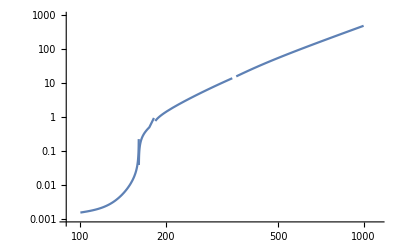

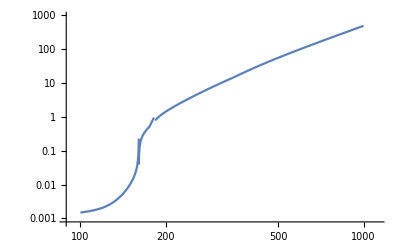

```mathematica
TotalWidthHiggs[Mh_] :=Re[WidthHuuBorn[Mh]+WidthHddBorn[Mh]+WidthHccBorn[Mh]+WidthHssBorn[Mh]+WidthHbbBorn[Mh]+WidthHττBorn[Mh]+WidthHμμBorn[Mh]+WidthHeeBorn[Mh]+ WidthHttBorn[Mh]+WidthHZγ[Mh]+TotalWidthHZZ[Mh]+TotalWidthHWW[Mh]+WidthHgg[Mh]+WidthHγγ[Mh]];
LogLogPlot[Re[TotalWidthHiggs[Mh]],{Mh,100,1000}]
TotalTreeWidth[Mh_]:= WidthHuuBorn[Mh]+WidthHddBorn[Mh]+WidthHccBorn[Mh]+WidthHssBorn[Mh]+WidthHbbBorn[Mh]+WidthHττBorn[Mh]+WidthHμμBorn[Mh]+WidthHeeBorn[Mh]+ WidthHttBorn[Mh]+TotalWidthHZZ[Mh]+TotalWidthHWW[Mh];
LogLogPlot[Re[TotalTreeWidth[Mh]],{Mh,100,1000}]
```

BBbar branching ratios

```mathematica
BranchingRatioBBbar[Mh_]:=WidthHbbBorn[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatioBBbar[Mh]],{Mh,100,1000}]
```

ττ Branching ratio

```mathematica
BranchingRatioττ[Mh_]:=WidthHττBorn[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatioττ[Mh]],{Mh,100,1000}]
```

gg branching ratio

```mathematica
BranchingRatiogg[Mh_]:=WidthHgg[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatiogg[Mh]],{Mh,100,1000}]
```

CCbar branching ratio

```mathematica
BranchingRatioCCbar[Mh_]:=WidthHccBorn[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatioCCbar[Mh]],{Mh,100,1000}]
```

γγ branching ratio

```mathematica
BranchingRatioγγ[Mh_]:=WidthHγγ[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatioγγ[Mh]],{Mh,100,1000}]
```

Ssbar branching ratio

```mathematica
BranchingRatioSSbar[Mh_]:=WidthHssBorn[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatioSSbar[Mh]],{Mh,100,1000}]
```

μμ branching ratio

```mathematica
BranchingRatioμμ[Mh_]:=WidthHμμBorn[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatioμμ[Mh]],{Mh,100,1000}]
```

Zγ branching ratio

```mathematica
BranchingRatioZγ[Mh_]:=WidthHZγ[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatioZγ[Mh]],{Mh,100,1000}]
```

WW branching ratio

```mathematica
BranchingRatioWW[Mh_]:=TotalWidthHWW[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatioWW[Mh]],{Mh,100,1000}]
```

ZZ Branching ratio

```mathematica
BranchingRatioZZ[Mh_]:=TotalWidthHZZ[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatioZZ[Mh]],{Mh,100,1000}]
```

TTbar Branching Ratio

```mathematica
BranchingRatioTTbar[Mh_]:=WidthHttBorn[Mh]/TotalWidthHiggs[Mh];
LogPlot[Re[BranchingRatioTTbar[Mh]],{Mh,100,1000}]
```

This is the cross section of production and decay of the Dilaton over the same for the Higgs

```mathematica
σggXγγOVERσggHγγ[f_,Mx_] := v^4/f^4 Rg[Mx]Rγ[Mx](TotalWidthHiggs[Mx])/(v^2/f^2 TotalTreeWidth[Mx]+WidthXγγ[Mx,f]+WidthXgg[Mx,f]) ;
σggXγγOVERσggHγγ[4000,200]
ContourPlot[σggXγγOVERσggHγγ[f_,Mx_],{Mx,20,200},{f,500,4500},Contours->{10,5,2,1,0.5,0.2,0.1},Exclusions-> None,MaxRecursion->3,PlotLegends->{"10","5","2","1","0.5","0.2","0.1"}]
Plot3D[σggXγγOVERσggHγγ[f,Mx],{Mx,20,1000},{f,500,4500}]
```

0.0151974+0.105889 ⅈ

-Graphics-

-Graphics3D-